```mathematica
Get["C:\\Universidad\\PRM\\PRM_22_23\\Practica 2\\drawTxPRM.m"]
```

```mathematica
(*Ver menu para dibujar*)? drawTxPRM`*
```

```mathematica
(*Datos*)
la=80;
mu=100;
nmuestras=1000;
```

```mathematica
(*Definimos FIFO*) Fifo[arri_,serv_]:=Module[{n,time},
n=0;
time=arri[[1]];
Map[(n++;If[time>=#,time+=serv[[n]],time=#+serv[[n]]])&,arri]]
```

```mathematica
(*Creamos funcion llegadas/servicio*)
```

```mathematica
RndExp[val_]:=-Log[RandomReal[]]/val//N;
```

```mathematica
(*Generamos llegadas y servicio*)
```

```mathematica
InterArrivals=Table[RndExp[la],nmuestras];
Arrivals=Accumulate[InterArrivals];
Servicios=Table[RndExp[mu],nmuestars];
Departures=Fifo[Arrivals,Servicios];
```

```mathematica
(*Calculamos los Injection times*)
```

```mathematica
InjectionTimes= Departures-Servicios;
```

```mathematica
(*Generamos los paquetes*)
```

```mathematica
listapaquetes=Table[{InjectionTimes[[n]],Servicios[[n]],n,0,0},{n,1,nmuestras}];
```

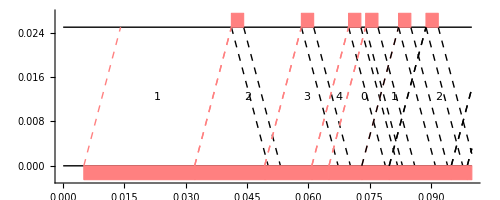

```mathematica
(*Hacemos set de la configuracion*)SetIniParDraw[0.009,0.003](*[tiempo_progpagacion,tiempo_supervision_ack]*)
Show[DrawWin[0,0.1,5], Map[(DrawPacketTx[#])&,listapaqueInjection]]
```